# Example 3 - Gamma distribution

Data

```mathematica
Data={0.8,1.1,1.2,1.4,1.8,2,4,5,8};
n=Length[Data];

xmean=Mean[Data];
g=GeometricMean[Data];
```

Hypotheses

```mathematica
alphaH=2.5;
muH=6;
sigma2H=2;
```

Normalizing constant

```mathematica
c= NIntegrate[((((y^x)/Gamma[x])*(g^x)*Exp[-xmean*y])^n)*(Sqrt[x*PolyGamma[1,x]-1]/y),{x,0.01,4},{y,0.01,5}];
```

Normalized Posterior distribution

```mathematica
gposterior=(1/c)*((((y^x)/Gamma[x])*(g^x)*Exp[-xmean*y])^n)*(Sqrt[x*PolyGamma[1,x]-1]/y);
```

```mathematica
NIntegrate[gposterior,{x,0.01,4},{y,0.01,5}]
```

1.

## Flat reference function [A]

```mathematica
gprofile1=(1/c)*((((y^alphaH)/Gamma[alphaH])*(g^alphaH)*Exp[-xmean*y])^n)*(Sqrt[alphaH*PolyGamma[1,alphaH]-1]/y);
```

```mathematica
FindMaximum[gprofile1,{y,1}]
```

{0.636742,{y→0.849802}}

Level

```mathematica
kFlatA=0.6367422340096495
```

0.636742

Region

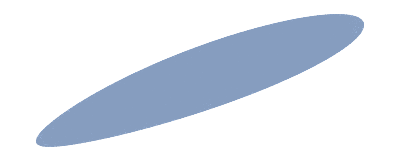

```mathematica
TbarFlatA=DiscretizeRegion[ImplicitRegion[gposterior>kFlatA,{x,y}],{{0.01,4},{0.01,5}},MaxCellMeasure->0.0001]
```

```mathematica
RegionPlot[TbarFlatA]
```

-Graphics-

```mathematica
TbarFlatAComplementary=DiscretizeRegion[ImplicitRegion[gposterior<=kFlatA,{x,y}],{{0.01,4},{0.01,2}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
f[x,y]:=(1/c)*((((y^x)/Gamma[x])*(g^x)*Exp[-xmean*y])^n)*(Sqrt[x*PolyGamma[1,x]-1]/y)
```

```mathematica
Integrate[f[x,y],{x,y}∈TbarFlatA]
```

0.557346

## Jeffreys prior as reference function [A]

Reference function

```mathematica
r=Sqrt[x*PolyGamma[1,x]-1]/y;
```

Surprise function

```mathematica
s=gposterior/r;
```

Profile function

```mathematica
sprofileA=(1/c)*((((y^alphaH)/Gamma[alphaH])*(g^alphaH)*Exp[-xmean*y])^n);
```

```mathematica
FindMaximum[sprofileA,{y,2}]
```

{1.16487,{y→0.889328}}

```mathematica
sstarA=1.1648652778361204
```

1.16487

Region

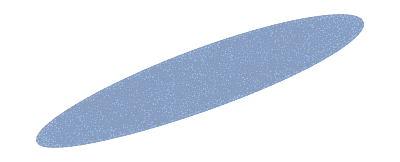

```mathematica
TbarJeffA=DiscretizeRegion[ImplicitRegion[s>sstarA,{x,y}],{{0.01,4},{0.01,5}},MaxCellMeasure->0.0001]
```

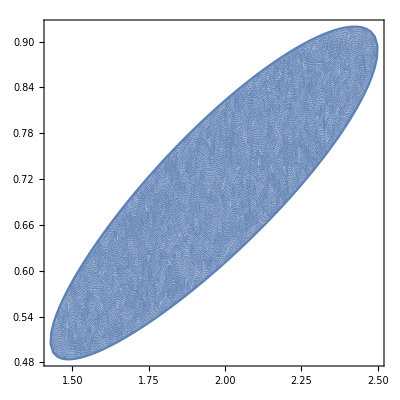

```mathematica
RegionPlot[TbarJeffA]
```

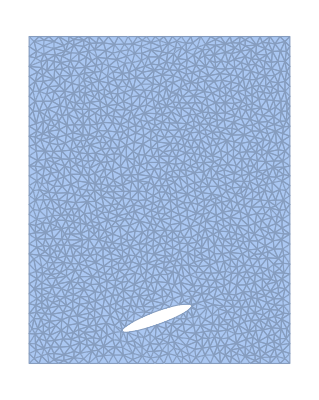

```mathematica
TbarJeffAComplementary=DiscretizeRegion[ImplicitRegion[s<=sstarA,{x,y}],{{0.01,4},{0.01,5}},MaxCellMeasure->0.01]
```

Integral

```mathematica
Integrate[f[x,y],{x,y}∈TbarJeffA]
```

0.185643

## Flat reference function [B]

```mathematica
yr=x/muH;
```

```mathematica
gprofile2=(1/c)*((((yr^alphaH)/Gamma[x])*(g^x)*Exp[-xmean*yr])^n)*(Sqrt[x*PolyGamma[1,x]-1]/yr);
```

```mathematica
FindMaximum[gprofile2,{x,4}]
```

{0.0376629,{x→3.2168}}

Level

```mathematica
kFlatB=0.03766294930544823
```

0.0376629

Region

```mathematica
TbarFlatB=DiscretizeRegion[ImplicitRegion[gposterior>kFlatB,{x,y}],{{0.01,5},{0.01,5}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarFlatB]
```

-Graphics-

```mathematica
TbarFlatBComplementary=DiscretizeRegion[ImplicitRegion[gposterior<=kFlatB,{x,y}],{{0.01,5},{0.01,5}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
Integrate[f[x,y],{x,y}∈TbarFlatB]
```

0.984287

## Jeffreys prior as reference function [B]

Reference function

```mathematica
r=Sqrt[x*PolyGamma[1,x]-1]/y;
```

Surprise function

```mathematica
s=gposterior/r;
```

```mathematica
yr=x/muH;
```

Profile function

```mathematica
sprofileB=(1/c)*((((yr^x)/Gamma[x])*(g^x)*Exp[-xmean*yr])^n);
```

```mathematica
FindMaximum[sprofileB,{x,1}]
```

{0.0760893,{x→1.1164}}

```mathematica
sstarB= 0.0760892931953657
```

0.0760893

Region

```mathematica
TbarJeffB=DiscretizeRegion[ImplicitRegion[s>=sstarB ,{x,y}],{{0.01,5},{0.01,3}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarJeffB]
```

-Graphics-

Integral

```mathematica
Integrate[f[x,y],{x,y}∈TbarJeffB]
```

0.962708

## Flat reference function [C]

```mathematica
yr=Sqrt[x/sigma2H];
```

```mathematica
gprofile3=(1/c)*((((yr^alphaH)/Gamma[x])*(g^x)*Exp[-xmean*yr])^n)*(Sqrt[x*PolyGamma[1,x]-1]/yr);
```

```mathematica
FindMaximum[gprofile3,{x,4}]
```

{0.298691,{x→2.27842}}

Level

```mathematica
kFlatC= 0.2986906281560602
```

0.298691

Region

```mathematica
TbarFlatC=DiscretizeRegion[ImplicitRegion[gposterior>kFlatC,{x,y}],{{0.01,5},{0.01,5}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarFlatC]
```

-Graphics-

```mathematica
TbarFlatCComplementary=DiscretizeRegion[ImplicitRegion[gposterior<=kFlatC,{x,y}],{{0.01,5},{0.01,5}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
Integrate[f[x,y],{x,y}∈TbarFlatC]
```

0.784088

## Jeffreys prior as reference function [C]

Reference function

```mathematica
r=Sqrt[x*PolyGamma[1,x]-1]/y;
```

Surprise function

```mathematica
s=gposterior/r;
```

```mathematica
yr=Sqrt[x/sigma2H];
```

Profile function

```mathematica
sprofileC=(1/c)*((((yr^x)/Gamma[x])*(g^x)*Exp[-xmean*yr])^n);
```

```mathematica
FindMaximum[sprofileC,{x,1}]
```

{0.631423,{x→2.68729}}

Level

```mathematica
sstarC= 0.6314231404041803
```

0.631423

Region

```mathematica
TbarJeffC=DiscretizeRegion[ImplicitRegion[s>sstarC ,{x,y}],{{0.01,5},{0.01,3}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarJeffC]
```

-Graphics-

Integral

```mathematica
Integrate[f[x,y],{x,y}∈TbarJeffC]
```

0.561975